```mathematica
Remove[d]
```

```mathematica
dϕext = ej^2/4*(1-(1-d^2)*Cos[ϕext]^2)
```

1/4 ej^2 (1-(1-d^2) Cos[ϕext]^2)

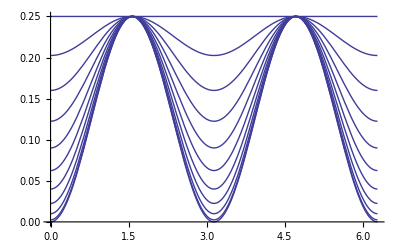

```mathematica
Plot[Map[dϕext /.{ej->1,d->#}& ,Range[0,1,0.1]],{ϕext,0,2π}]
```

```mathematica
dϕextp= Sqrt[ejs*2ec*Abs[Sin[ϕext/2]*Tan[ϕext/2]]]
```

√2 √(ec ejs) √Abs[Sin[ϕext/2] Tan[ϕext/2]]

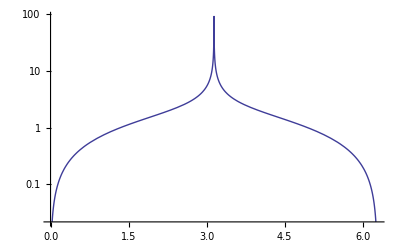

```mathematica
LogPlot[dϕextp /.{ejs->1,ec->1},{ϕext,0,2π}]
```